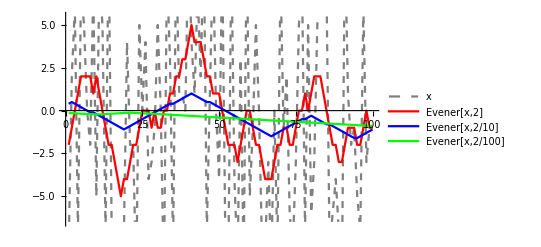

-44

```mathematica
Evener[inputList_,tolerance_]:=Module[{l=inputList,i,Δ=Table[0,Length[l]],t=tolerance},
Until[Δ==Table[0,Length[l]],
Δ=Table[0,Length[l]];
For[i=1,i<Length[l],i++,
If[l[[i]]-l[[i+1]]>=t,
Δ[[i]]+=-t/2;
Δ[[i+1]]+=t/2
];
If[l[[i+1]]-l[[i]]>=t,
Δ[[i]]+=t/2;
Δ[[i+1]]+=-t/2
]
];
l=l+Δ
];
Return[l]
]
n=100;
k=10;
x=Table[RandomInteger[{-k,k}],n];
ListLinePlot[{x,Evener[x,2],Evener[x,2/10],Evener[x,2/100]},PlotLegends->{"x","Evener[x,2]","Evener[x,2/10]","Evener[x,2/100]"},PlotStyle->{{Gray,Dashed},Red,Blue,Green}]
Total[x]
```